```mathematica
{β=0.25,α = .0025};
(*s'[t]= -β s[t] i[t];
i'[t]= β s[t] i[t] - α i[t];
r'[t]= α i[t];
sα'[t]= -β *(i[t]*sα[t]+s[t]*iα[t]);
sβ'[t]=-s[t]*i[t]-β*(sβ[t]+s[t]*iβ[t]);
ia'[t]=β*(i[t]*sα[t]+s[t]*iα[t])-i[t]-α[t]*iβ[t];
iβ'[t]=s[t]*i[t]+β*(s[t]*iβ[t]+i[t]*sβ[t])-α*iβ[t];
rα'[t]=α+α*iα[t];
rβ'[t]=α*iβ[t];*)
sol= Flatten[ NDSolve[{
s'[t]== -β*s[t]* i[t],s[0]==.9,
i'[t]== β*s[t]* i[t] - α *i[t],i[0]==.1,
r'[t]== α *i[t],r[0]==0,
sα'[t]== -β *(i[t]*sα[t]+s[t]*iα[t]),sα[0]==0,sβ'[t]==-s[t]*i[t]-β*(i[t]*sβ[t]+s[t]*iβ[t]),sβ[0]==0,iα'[t]==β*(i[t]*sα[t]+s[t]*iα[t])-i[t]-α*iα[t],iα[0]==1,iβ'[t]==s[t]*i[t]+β*(s[t]*iβ[t]+i[t]*sβ[t])-α*iβ[t],iβ[0]==0,
rα'[t]==i[t]+α*iα[t],rα[0]==0,
rβ'[t]==α*iβ[t],rβ[0]==0},
{s,i,r,sα,sβ,iα,iβ,rα,rβ},{t,0,100}]]
```

{s→InterpolatingFunction[{{0., 100.}}, <>],i→InterpolatingFunction[{{0., 100.}}, <>],r→InterpolatingFunction[{{0., 100.}}, <>],sα→InterpolatingFunction[{{0., 100.}}, <>],sβ→InterpolatingFunction[{{0., 100.}}, <>],iα→InterpolatingFunction[{{0., 100.}}, <>],iβ→InterpolatingFunction[{{0., 100.}}, <>],rα→InterpolatingFunction[{{0., 100.}}, <>],rβ→InterpolatingFunction[{{0., 100.}}, <>]}

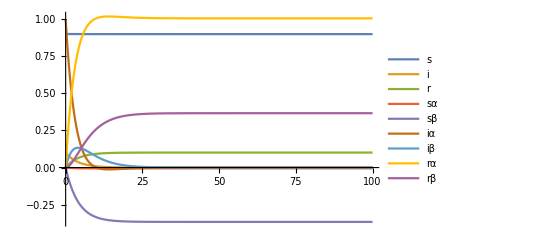

```mathematica
Plot[Release[{s[t],i[t],r[t],sα[t],sβ[t],iα[t],iβ[t],rα[t],rβ[t]} //. sol ], {t, 0, 100},PlotLegends->{"s","i","r","sα","sβ","iα","iβ","rα","rβ"}]
```

```mathematica
sol2= Flatten[ NDSolve[{
s'[t]== -β*s[t]* i[t],s[0]==.9,
i'[t]== β*s[t]* i[t] - α *i[t],i[0]==.1,
r'[t]== α *i[t],r[0]==0,
sα'[t]== -β *(i[t]*sα[t]+s[t]*iα[t]),sα[0]==0,sβ'[t]==-s[t]*i[t]-β*(i[t]*sβ[t]+s[t]*iβ[t]),sβ[0]==0,iα'[t]==β*(i[t]*sα[t]+s[t]*iα[t])-i[t]-α*iα[t],iα[0]==0,iβ'[t]==s[t]*i[t]+β*(s[t]*iβ[t]+i[t]*sβ[t])-α*iβ[t],iβ[0]==1,
rα'[t]==i[t]+α*iα[t],rα[0]==0,
rβ'[t]==α*iβ[t],rβ[0]==0},
{s,i,r,sα,sβ,iα,iβ,rα,rβ},{t,0,100}]]
```

{s→InterpolatingFunction[{{0., 100.}}, <>],i→InterpolatingFunction[{{0., 100.}}, <>],r→InterpolatingFunction[{{0., 100.}}, <>],sα→InterpolatingFunction[{{0., 100.}}, <>],sβ→InterpolatingFunction[{{0., 100.}}, <>],iα→InterpolatingFunction[{{0., 100.}}, <>],iβ→InterpolatingFunction[{{0., 100.}}, <>],rα→InterpolatingFunction[{{0., 100.}}, <>],rβ→InterpolatingFunction[{{0., 100.}}, <>]}

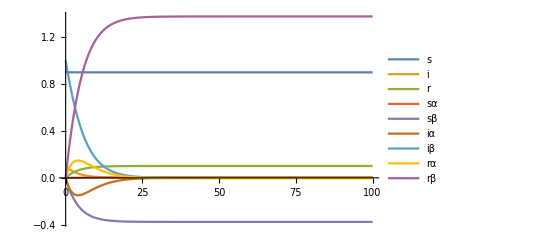

```mathematica
Plot[Release[{s[t],i[t],r[t],sα[t],sβ[t],iα[t],iβ[t],rα[t],rβ[t]} //. sol2 ], {t, 0, 100},PlotLegends->{"s","i","r","sα","sβ","iα","iβ","rα","rβ"}]
```